# Hermite Curve

```mathematica
G = {{0,0}, {40,0}, {20,20}, {20,20}};
```

```mathematica
M = {{2, -3, 0, 1}, {-2, 3, 0, 0}, {1, -2, 1, 0}, {1, -1, 0, 0}};
T = {t^3, t^2, t, 1};
```

```mathematica
hermite = Transpose[G].M.Transpose[T];
hermite//MatrixForm
```

(20 t+60 t^2-40 t^3
20 t-60 t^2+40 t^3)

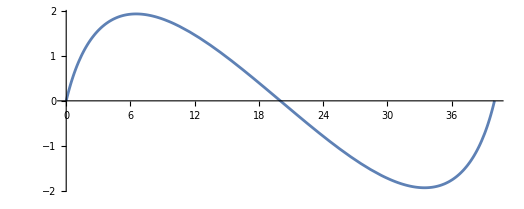

```mathematica
ParametricPlot[hermite /. t->u, {u,0,1}]
```

```mathematica
GList = {{{161, 244}, {141, 290}, {-39.51, 38.433}, {-0.174, 54.234}},
		{{141, 290}, {150, 329}, {15.072, 59.061}, {11.928, 57.939}},
		{{150, 329}, {147, 331}, {-2.676, 2.826}, {-3.648, -0.561}},
		{{163, 307}, {147, 331}, {10.881, 32.259}, {-34.968, 7.617}},
		{{163, 317}, {203, 387}, {-3.66, 80.802}, {28.845, 61.563}},
		{{174, 253}, {203, 331}, {-46.617, 86.919}, {72.411, 53.307}},
		{{244, 243}, {266, 286}, {36.201, 33.795}, {3.678, 51.723}},
		{{266, 286}, {256, 327}, {-3.954, 36.978}, {-7.308, 37.65}},
		{{256, 327}, {259, 331}, {2.025, 5.55}, {3.486, 3.423}},
		{{244, 307}, {260, 331}, {-6.906, 35.031}, {33.456, 13.395}},
		{{244, 316}, {203, 387}, {4.92, 82.221}, {-32.574, 61.557}},
		{{231, 253}, {203, 331}, {54.516, 86.925}, {-69.585, 53.838}}
};
```

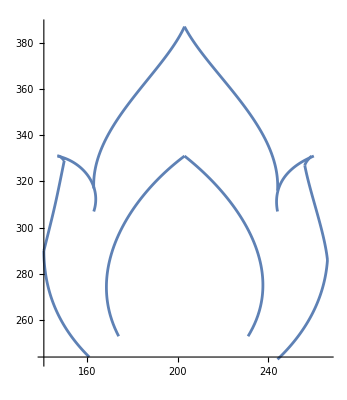

```mathematica
Show[
	Table[ParametricPlot[Transpose[GList[[i]]].M.Transpose[T] /. t->u, {u,0,1}] ,{i, Length[GList]}], PlotRange->All
]
```